```mathematica
(*runned with CVnoisyStorageRates !! *)
(*BmajTable=Table[{delta,BMa[1.001,delta]},{delta,0.1,3,0.1}]*)
```

```mathematica
BmajTable={{0.1,3.2350809115302477},{0.2,2.7269852515182578},{0.30000000000000004,2.4218112102210907},{0.4,2.2012334582614796},{0.5,2.0263714101532195},{0.6,1.8816120235368385},{0.7000000000000001,1.756731352688302},{0.8,1.6473493158496557},{0.9,1.5491707093200082},{1.,1.4601484496649344},{1.1,1.3780590333430203},{1.2000000000000002,1.3023802017841206},{1.3000000000000003,1.2318389840099302},{1.4000000000000001,1.1656819180764986},{1.5000000000000002,1.1033219768430216},{1.6,1.0459747705505003},{1.7000000000000002,0.9903847337364288},{1.8000000000000003,0.9374723823555294},{1.9000000000000001,0.8870211059662146},{2.,0.8388626512678995},{2.1,0.792856164788472},{2.2,0.7488485658540781},{2.3000000000000003,0.7066539266396925},{2.4000000000000004,0.6660658800441215},{2.5000000000000004,0.6268734696677143},{2.6,0.5888851437183347},{2.7,0.551951224590625},{2.8000000000000003,0.5159778620192572},{2.9000000000000004,0.4809314933960935},{3.0000000000000004,0.4468320642641711}};
BmajFu=Interpolation[BmajTable];

 

(*EC efficiency for below is 1 and for a state with losses of 6 db on one side. 
If you need it for different parameters you have to generate the ECTable again with command: 

ECTable=Table[{delta,EC[delta,EPRlossB[6,0.95,0.001],1]},{delta,0.2,3,0.1}]
 *)
ECTable={{0.05,5.271369447880514},{0.1,4.271369447880513},{0.15000000000000002,3.6864069471593575},{0.2,3.2713694478805135},{0.30000000000000004,2.7344273697578068},{0.4,2.354606053568536},{0.5,2.075515209964439},{0.6000000000000001,1.8615222470473487},{0.7,1.6929721464692733},{0.8,1.557620751697851},{0.9000000000000001,1.4471171768433484},{1.,1.3553774511501748},{1.1,1.2778312281972304},{1.2,1.2110519692969453},{1.3,1.152517262964976},{1.4000000000000001,1.1004067796776758},{1.5,1.053423286001144},{1.6,1.0106426334307432},{1.7,0.9713971688311975},{1.8,0.9351910809436057},{1.9000000000000001,0.9016426767484704},{2.,0.8704468795733544},{2.1,0.841343828040189},{2.2,0.8141411684257376},{2.3000000000000003,0.7886387895953724},{2.4000000000000004,0.7646787474440604},{2.5000000000000004,0.7421213990883366},{2.6000000000000005,0.7208431649770695},{2.7,0.700734497385936},{2.8000000000000003,0.6816980105237012},{2.9000000000000004,0.6636469070177755},{3.0000000000000004,0.6465035652638065}};
ECFu1=Interpolation[ECTable];
ECFun[d_]:=ECApp[d,EPRlossB[6,0.95,0.001],1];

(*LTypTable=Table[{delta,LTyp[6,0.95,0.001,delta]},{delta,0.1,3,0.1}]*)
(*not required for the UR Plot *) 
LTypTable={{0.1,4.277788635581731},{0.2,3.298994194858672},{0.30000000000000004,2.7396753371782285},{0.4,2.3590445159001314},{0.5,2.079022659638575},{0.6,1.8640327044954477},{0.7000000000000001,1.6944690109704874},{0.8,1.5581313177408171},{0.9,1.4467093748866358},{1.,1.3541514650189983},{1.1,1.2759044439883351},{1.2000000000000002,1.2085422313057785},{1.3000000000000003,1.1495306697051149},{1.4000000000000001,1.097031738817435},{1.5000000000000002,1.0497296493343642},{1.6,1.0066839324293269},{1.7000000000000002,0.967214126909477},{1.8000000000000003,0.9308150588616719},{1.9000000000000001,0.8970985527647648},{2.,0.8657551672234294},{2.1,0.8365207621721087},{2.2,0.8092042530830645},{2.3000000000000003,0.7836013515944198},{2.4000000000000004,0.7595531330176417},{2.5000000000000004,0.7369189796567355},{2.6,0.715574430842254},{2.7,0.6954090761452738},{2.8000000000000003,0.6763247483683836},{2.9000000000000004,0.6582338892266717},{3.0000000000000004,0.6410581343197084}};
LTypFu1=Interpolation[LTypTable];
LTypFun[d_]:=LTypApp[6,0.95,0.001,d];
```

InterpolatingFunction::dmval: Input value {0.0000510714} lies outside the range of data in the interpolating function. Extrapolation will be used.

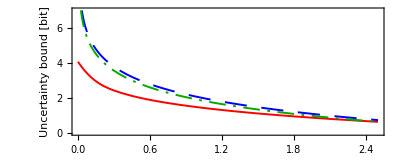

```mathematica
URPlot=Plot[{BmajFu[d],λG[1.001,d,10^8,10^(-7)],Biid[d,10^8,EPRlossB[6,0.95,0.001],10,10^(-7)]},{d,0,2.5},AspectRatio->0.4,PlotRange->{0,7},
LabelStyle->Directive[Black,FontSize->10],PlotStyle->{{Thickness[0.0035],Red},{Thickness[0.0035],Blue,Dashing[{0.04,0.0263}]} ,{Thickness[0.0035],Darker[Green],Dashing[{0.03,0.0135,0.005,0.0135}]},{Thickness[0.0035],Purple,Dashed},{Thick,Black,Dashed}},
FrameStyle->Thickness[0.003],Frame->{{True,True},{True,True}},FrameLabel-> {"Discretization bin size δ", "Uncertainty bound [bit]"},
BaseStyle->{FontFamily->"Times New Roman",FontSize->16}]
```

```mathematica
Export["UncertaintyBounds.pdf",URPlot]
```